# Neural Network Implementation

## Function Definitions

#### Network basics

```mathematica
(* initialize new linear layer with randomly distributed weights and biases *)
linearLayer[inputs_, neurons_, OptionsPattern[]] :=
	<|
		"Inputs" -> inputs,
		"Neurons" -> neurons,
		"Weights" -> RandomVariate[OptionValue["WeightDistribution"], {neurons, inputs}],
		"Biases" -> RandomVariate[OptionValue["BiasDistribution"], neurons],
		"ActivationFunction" -> OptionValue["ActivationFunction"]
	|>

Options[linearLayer] = {
	"ActivationFunction" -> LogisticSigmoid,
	"WeightDistribution" -> NormalDistribution[0, 1],
	"BiasDistribution" -> UniformDistribution[{0,0}]
};
```

```mathematica
(* apply weighted summation from layer *)
applyLinearLayer[layer_, inputs_] :=
	layer["Weights"] . inputs + layer["Biases"]
```

```mathematica
(* apply activation function from layer *)
applyActivation[layer_, inputs_] :=
	layer["ActivationFunction"] /@ inputs
```

```mathematica
(* feed inputs forward through each layer, sowing summations and activations *)
applyForwardPass[layers_, inputs_] :=
	Fold[
		Function[{current, layer},
			Sow[applyLinearLayer[layer, current], "Summations"] //
			Sow[applyActivation[layer, #], "Activations"] &
		],
		inputs,
		layers
	]
```

```mathematica
(* reap intermediates and return association with outputs, summations, and activations *)
reapForwardPass[layers_, inputs_] :=
	Reap[
		"Outputs" -> applyForwardPass[layers, inputs],
		{"Summations", "Activations"},
		Rule
	] // Flatten // Apply[Association]
```

#### Backpropagation

```mathematica
(* calculate loss for single training example using SSE *)
calculateLoss[output_, target_, "SumSquaredError"] :=
	Total[(output - target) ^ 2]
```

```mathematica
(* neuron deltas for output layer (d Error d Summation) *)
calculateOutputDeltas[output_, target_, summations_, activationFunction_, "SumSquaredError"] :=
	(output - target) * (activationFunction' /@ summations)
```

```mathematica
(* backpropagate deltas through one layer with chain rule *)
(* takes deltas and weights from next layer, activation and summations from current layer *)
calculateNextDeltas[nextDeltas_, weights_, activationFunction_, summations_] :=
	(nextDeltas . weights) * (activationFunction' /@ summations)
```

```mathematica
(* backpropagate output deltas through all layers *)
backpropagateDeltas[outputDeltas_, layers_, fp_] :=

	(* take activations and summations from all but last layer, weights from all but first layer *)
	With[{
			weights = Rest[Lookup[layers, "Weights"]],
			activationFunctions = Most[Lookup[layers, "ActivationFunction"]],
			summations = Most[fp["Summations"]]
		},

		(* fold layer parameters into neuron delta calculation in reverse *)
		FoldList[
			calculateNextDeltas[#1, Sequence @@ #2] &,
			outputDeltas,
			MapThread[List, {weights, activationFunctions, summations}] // Reverse
		] // Reverse
	]
```

```mathematica
(* calculate error gradients wrt weights from error gradients wrt summations *)
calculateWeightGradients[allDeltas_, inputs_, allActivations_] :=
	MapThread[
		Function[{deltas, activations},
			Transpose[{deltas}] . {activations}
		],
		{allDeltas, Prepend[Most @ allActivations, inputs]}
	]
```

```mathematica
(* calculate all neuron deltas and weight gradients by backpropagating errors *)
backwardPass[layers_, labelledInput_Rule, lossFunction_ : "SumSquaredError"] :=
	Module[{forwardPass, outputDeltas, allDeltas, weightGradients},
	
		forwardPass = reapForwardPass[layers, First @ labelledInput];
		
		outputDeltas = calculateOutputDeltas[
			forwardPass["Outputs"],
			Last[labelledInput],
			Last[forwardPass["Summations"]],
			Last[layers]["ActivationFunction"],
			lossFunction
		];
		
		allDeltas = backpropagateDeltas[outputDeltas, layers, forwardPass];
		
		weightGradients = calculateWeightGradients[
			allDeltas,
			First @ labelledInput,
			forwardPass["Activations"]
		];
		
		<|"AllDeltas" -> allDeltas, "WeightGradients" -> weightGradients|>
	]
```

#### Training

```mathematica
(* accumulate gradients over multiple pieces of data for batch training *)
accumulateGradients[layers_, data_, lossFunction_] :=
	With[{gradients = Map[backwardPass[layers, #, lossFunction] &, data]},
		<|
			"WeightGradients" -> Total[Lookup[gradients, "WeightGradients"]],
			"AllDeltas" -> Total[Lookup[gradients, "AllDeltas"]]
		|>
	]
```

```mathematica
(* update weights to reduce overall loss according to weight gradients and learning rate *)
(* note: currently uses same learning rate for bias and weight updates *)
gradientDescentStep[layers_, gradients_, learningRate_] :=
	MapThread[
		Function[{layer, weightGradients, allDeltas},
			Append[layer, {
				"Weights" -> layer["Weights"] - weightGradients * learningRate,
				"Biases" -> layer["Biases"] - allDeltas * learningRate
			}]
		],
		{layers, gradients["WeightGradients"], gradients["AllDeltas"]}
	]
```

```mathematica
(* split data into batches *)
batchData[data_, batchSize_] :=
	Partition[RandomSample[data], UpTo[batchSize]]
```

```mathematica
(* update network based on one full pass through batched data *)
trainEpoch[layers_List, trainingData_List, OptionsPattern[trainNetwork]] :=
	Fold[
		Function[{currentLayers, currentBatch},
			gradientDescentStep[
				currentLayers,
				accumulateGradients[currentLayers, currentBatch, OptionValue["LossFunction"]],
				OptionValue["LearningRate"]
			]
		],
		layers,
		batchData[trainingData, OptionValue["BatchSize"]]
	]
```

```mathematica
(* apply network to make labelled predictions for each input *)
makePredictions[layers_, inputs_] :=
	AssociationMap[
		applyForwardPass[layers, #] &,
		inputs
	]
```

```mathematica
(* train network, returning final result only *)
trainNetwork[initialLayers_List, trainingData_List, opts : OptionsPattern[]] :=
	Nest[
		Sow[trainEpoch[#, trainingData, opts]] &, 
		initialLayers,
		OptionValue["Epochs"]
	] // Reap // trainingProgress[#, trainingData, OptionValue["LossFunction"], OptionValue["ShowProgress"]] &
	
Options[trainNetwork] = {
	"LearningRate" -> .1,
	"LossFunction" -> "SumSquaredError", (* change this option for red outputs *)
	"BatchSize" -> 1,
	"Epochs" -> 1,
	"ShowProgress" -> True
};
```

```mathematica
(* calculate total loss over all labelled inputs *)
calculateTotalLoss[layers_, labelledInputs_, lossFunction_ : OptionValue[trainNetwork, "LossFunction"]] :=
	Map[
		Function[labelledInput,
			calculateLoss[
				applyForwardPass[layers, First @ labelledInput],
				Last @ labelledInput,
				lossFunction
			]
		],
		labelledInputs
	] // Total
```

```mathematica
(* graph training loss across epochs *)
trainingProgress[training_, trainingData_, lossFunction_, showProgress_ /; TrueQ[showProgress]] :=
	(* reap intermediate networks from training to track progress *)
	Module[{networks, trainingLoss},
	
		networks = training // Rest // Flatten[#, 2] &;
		trainingLoss = Map[calculateTotalLoss[#, trainingData, lossFunction] &, networks];
		
		ListLinePlot[
			trainingLoss,
			Frame -> True,
			FrameLabel -> {"Epochs", "Loss"},
			PlotRange -> All
		] // CellPrint;
		
		Last @ networks
	]

(* return final network only if "ShowProgress" option is False *)
trainingProgress[training_, trainingData_, lossFunction_, showProgress_ /; !TrueQ[showProgress]] :=
	First @ training
```

## Example: Learning XOR

#### Setup learning parameters

```mathematica
learningRate = 1;
lossFunction = "SumSquaredError";
batchSize = 1;
epochs =5000;
```

#### Build training dataset

```mathematica
inputs = {{0,0},{0,1},{1,0},{1,1}};
targets = List /@ {0,1,1,0};
```

```mathematica
trainingData = MapThread[Rule, {inputs, targets}];
```

#### Create network with randomly initialized layers

```mathematica
network = {linearLayer[2, 2],linearLayer[2, 1]}
```

{<|Inputs→2,Neurons→2,Weights→{{-0.505963,0.548416},{-1.81138,2.58433}},Biases→{0.,0.},ActivationFunction→LogisticSigmoid|>,<|Inputs→2,Neurons→1,Weights→{{-0.937359,0.496544}},Biases→{0.},ActivationFunction→LogisticSigmoid|>}

#### Make predictions with untrained network

```mathematica
makePredictions[network, inputs]
```

<|{0,0}→{0.44512},{0,1}→{0.466958},{1,0}→{0.429761},{1,1}→{0.465328}|>

```mathematica
calculateTotalLoss[network, trainingData]
```

1.02397

#### Train network

```mathematica
trainedNetwork = trainNetwork[
network,
trainingData, 
"LearningRate"-> learningRate,
"LossFunction" -> lossFunction,
"BatchSize" -> batchSize,
"Epochs"->epochs,
"ShowProgress"->True]
```

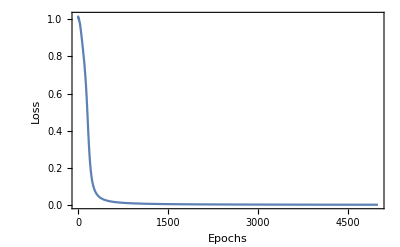

{<|Inputs→2,Neurons→2,ActivationFunction→LogisticSigmoid,Weights→{{-5.81862,6.02587},{-6.23343,6.12447}},Biases→{2.91664,-3.32106}|>,<|Inputs→2,Neurons→1,ActivationFunction→LogisticSigmoid,Weights→{{-9.32028,9.58544}},Biases→{4.4284}|>}

#### Make predictions from trained network

```mathematica
makePredictions[trainedNetwork, inputs]
```

<|{0,0}→{0.0166379},{0,1}→{0.984435},{1,0}→{0.980996},{1,1}→{0.0147959}|>

```mathematica
calculateTotalLoss[trainedNetwork, trainingData]
```

0.00109916